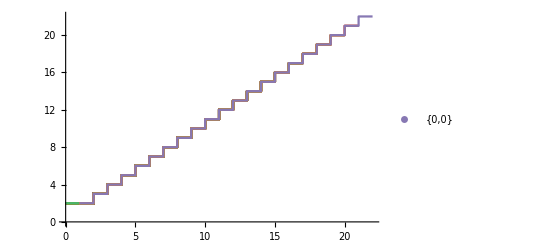
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Table[ListStepPlot[Legended[FlattenAt[
 Table[
Style[Text[
With[
{
graph = NestGraph[
ReplaceList[{
{0,left___,left___,s___}:>{s,0,0},
{1,left___,left___,s___}:>{s,1,1,0,1}
}],
{Tuples[{0,1},lengthInitialCondition][[indexInitialConditionWithGivenLength]]},
timeStep,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"
]
},
Table[
Length /@FindShortestPath[graph,First[VertexList[graph]],VertexList[graph][[i]]],
{i,1,Length[VertexList[graph]]}
]
]]][[1]][[1]],
{timeStep,1,20}
]
,
{#}&/@Range[20]],Tuples[{0,1},lengthInitialCondition][[indexInitialConditionWithGivenLength]]]],
{lengthInitialCondition,2,3},
{indexInitialConditionWithGivenLength,1,2^lengthInitialCondition}]
```

```mathematica
Table[ListStepPlot[Legended[FlattenAt[
 Table[
Style[Text[
With[
{
graph = NestGraph[
ReplaceList[{
{0,left___,left___,s___}:>{s,0,0},
{1,left___,left___,s___}:>{s,1,1,0,1}
}],
{Tuples[{0,1},lengthInitialCondition][[indexInitialConditionWithGivenLength]]},
timeStep,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"
]
},
Table[
Length /@FindShortestPath[graph,First[VertexList[graph]],VertexList[graph][[i]]],
{i,1,Length[VertexList[graph]]}
]
]]][[1]][[1]],
{timeStep,1,50}
]
,
{#}&/@Range[50]],Tuples[{0,1},lengthInitialCondition][[indexInitialConditionWithGivenLength]]]],
{lengthInitialCondition,2,3},
{indexInitialConditionWithGivenLength,1,2^lengthInitialCondition}]
```

$Aborted